```mathematica
$Assumptions={n>0,a>0,d>0,q>0,t>0,z>0,w>0,α>0,β>0,k>0,NN>0,σ>0,s>0,z∈ Reals,px2∈ Reals,py2∈ Reals,px1∈ Reals,py1∈ Reals,px∈ Reals,py∈ Reals,r∈ Reals,r1∈ Reals,r2∈ Reals,x1∈ Reals,x2∈ Reals,x∈ Reals,w∈ Reals,t∈ Reals,k1∈ Reals,k2∈ Reals,k∈ Reals,n∈ Reals,q∈ Reals,a∈ Reals,d∈ Reals,p∈ Reals,p1∈ Reals,p2∈ Reals,y1∈Reals,y2∈Reals,α∈Reals,β∈Reals,σ∈Reals,s∈Reals,NN∈Reals,k∈Reals}
```

{n>0,a>0,d>0,q>0,t>0,z>0,w>0,α>0,β>0,k>0,NN>0,σ>0,s>0,z∈Reals,px2∈Reals,py2∈Reals,px1∈Reals,py1∈Reals,px∈Reals,py∈Reals,r∈Reals,r1∈Reals,r2∈Reals,x1∈Reals,x2∈Reals,x∈Reals,w∈Reals,t∈Reals,k1∈Reals,k2∈Reals,k∈Reals,n∈Reals,q∈Reals,a∈Reals,d∈Reals,p∈Reals,p1∈Reals,p2∈Reals,y1∈Reals,y2∈Reals,α∈Reals,β∈Reals,σ∈Reals,s∈Reals,NN∈Reals,k∈Reals}

```mathematica
(√(k/z))/(√(2 π))ⅇ^(-(ⅈ π)/4+ⅈ k z)Integrate[((ⅇ^(-(-d+xp)^2/(4 σ^2)))/((2 π)^(1/4) √σ)+(ⅇ^(-(d+xp)^2/(4 σ^2)))/((2 π)^(1/4) √σ))ⅇ^((ⅈ k (x-xp)^2)/(2 z)),{xp,-∞,∞}]
```

(ⅇ^(-(ⅈ π)/4+ⅈ k z-(k (d^2+x^2))/(ⅈ z+2 k σ^2)) (ⅇ^((k (d-x)^2)/(2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(2 ⅈ z+4 k σ^2))) (2/π)^(1/4) √(k/z))/(√(1/σ-(2 ⅈ k σ)/z))

```mathematica
FullSimplify[((ⅇ^(-(ⅈ π)/4+ⅈ k z-(k (d^2+x^2))/(ⅈ z+2 k σ^2)) (ⅇ^((k (d-x)^2)/(2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(2 ⅈ z+4 k σ^2))) (2/π)^(1/4) √(k/z))/(√(1/σ-(2 ⅈ k σ)/z)))((ⅇ^((ⅈ π)/4-ⅈ k z-(k (d^2+x^2))/(-ⅈ z+2 k σ^2)) (ⅇ^((k (d-x)^2)/(-2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(-2 ⅈ z+4 k σ^2))) (2/π)^(1/4) √(k/z))/(√(1/σ+(2 ⅈ k σ)/z)))]
```

(√2 ⅇ^(-(4 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) (ⅇ^((k (d-x)^2)/(-2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(-2 ⅈ z+4 k σ^2))) (ⅇ^((k (d-x)^2)/(2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(2 ⅈ z+4 k σ^2))) k σ)/(√(π z^2+4 k^2 π σ^4))

```mathematica
Integrate[(√2 ⅇ^(-(4 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) (ⅇ^((k (d-x)^2)/(-2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(-2 ⅈ z+4 k σ^2))) (ⅇ^((k (d-x)^2)/(2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(2 ⅈ z+4 k σ^2))) k σ)/(√(π z^2+4 k^2 π σ^4)),{x,-∞,∞}]
```

2+2 ⅇ^(-d^2/(2 σ^2))

```mathematica
FullSimplify[((√2 ⅇ^(-(4 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) (ⅇ^((k (d-x)^2)/(-2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(-2 ⅈ z+4 k σ^2))) (ⅇ^((k (d-x)^2)/(2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(2 ⅈ z+4 k σ^2))) k σ)/(√(π z^2+4 k^2 π σ^4)))/(2+2 ⅇ^(-d^2/(2 σ^2)))]
```

(√2 ⅇ^(-(4 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) (ⅇ^((k (d-x)^2)/(-2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(-2 ⅈ z+4 k σ^2))) (ⅇ^((k (d-x)^2)/(2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(2 ⅈ z+4 k σ^2))) k σ)/((2+2 ⅇ^(-d^2/(2 σ^2))) √(π z^2+4 k^2 π σ^4))

```mathematica
Integrate[(√2 ⅇ^(-(4 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) (ⅇ^((k (d-x)^2)/(-2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(-2 ⅈ z+4 k σ^2))) (ⅇ^((k (d-x)^2)/(2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(2 ⅈ z+4 k σ^2))) k σ)/((2+2 ⅇ^(-d^2/(2 σ^2))) √(π z^2+4 k^2 π σ^4)),{x,-∞,∞}]
```

1

```mathematica
(√2 ⅇ^(-(4 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) (Simplify[ⅇ^((k (d-x)^2)/(-2 ⅈ z+4 k σ^2))ⅇ^((k (d-x)^2)/(2 ⅈ z+4 k σ^2))]+Simplify[ⅇ^((k (d+x)^2)/(-2 ⅈ z+4 k σ^2))ⅇ^((k (d-x)^2)/(2 ⅈ z+4 k σ^2))]+Simplify[ⅇ^((k (d-x)^2)/(-2 ⅈ z+4 k σ^2))ⅇ^((k (d+x)^2)/(2 ⅈ z+4 k σ^2))]+Simplify[ⅇ^((k (d+x)^2)/(-2 ⅈ z+4 k σ^2))ⅇ^((k (d+x)^2)/(2 ⅈ z+4 k σ^2))])  k σ)/((2+2 ⅇ^(-d^2/(2 σ^2))) √(π z^2+4 k^2 π σ^4))
```

```mathematica
(√2 ⅇ^(-(4 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) (ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4))+ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4))+ⅇ^((2 k (d^2 k σ^2+k x^2 σ^2))/(z^2+4 k^2 σ^4))ExpToTrig[(ⅇ^((2 k (-ⅈ d x z))/(z^2+4 k^2 σ^4))+ⅇ^((2 k (ⅈ d x z))/(z^2+4 k^2 σ^4)))]) k σ)/((2+2 ⅇ^(-d^2/(2 σ^2))) √(π z^2+4 k^2 π σ^4))
```

(√2 ⅇ^(-(4 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) k σ (ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4))+ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4))+2 ⅇ^((2 k (d^2 k σ^2+k x^2 σ^2))/(z^2+4 k^2 σ^4)) Cos[(2 d k x z)/(z^2+4 k^2 σ^4)]))/((2+2 ⅇ^(-d^2/(2 σ^2))) √(π z^2+4 k^2 π σ^4))

```mathematica
FullSimplify[(√2 ⅇ^(-(4 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) k σ (ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4))+ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4))+2 ⅇ^((2 k (d^2 k σ^2+k x^2 σ^2))/(z^2+4 k^2 σ^4)) Cos[(2 d k x z)/(z^2+4 k^2 σ^4)]))/((2+2 ⅇ^(-d^2/(2 σ^2))) √(π z^2+4 k^2 π σ^4))]
```

(√2 ⅇ^(-(4 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) k σ (ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4))+ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4))+2 ⅇ^((2 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) Cos[(2 d k x z)/(z^2+4 k^2 σ^4)]))/((2+2 ⅇ^(-d^2/(2 σ^2))) √(π z^2+4 k^2 π σ^4))

```mathematica
themonkey4[x_,z_,d_,k_,σ_] := (√2 ⅇ^(-(4 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) k σ (ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4))+ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4))+2 ⅇ^((2 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) Cos[(2 d k x z)/(z^2+4 k^2 σ^4)]))/((2+2 ⅇ^(-d^2/(2 σ^2))) √(π z^2+4 k^2 π σ^4))
```

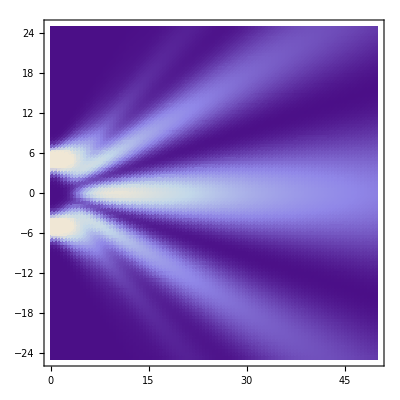

```mathematica
DensityPlot[themonkey4[x,t,5,1,1],{t,0,50},{x,-25,25},PlotPoints->{100,100},PlotRange->{Full,Full,{0,0.1}},ClippingStyle->Automatic,BaseStyle->{FontFamily->"Times",FontSize->14},AspectRatio->1]
```

```mathematica
yyynewBes2[x_,y_,t_,k_,w_]:=Sum[(BesselJ[0,k √(x^2+(y-d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y-d)^2)] Sin[w t]+BesselJ[0,k √(x^2+(y+d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y+d)^2)] Sin[w t])/(2 6),{d,3,7,0.5}]
```

```mathematica
DensityPlot[yyynewBes2[x,y,0,1,1],{x,0,50},{y,-25,25},PlotPoints->{200,200},ClippingStyle->Automatic]
```

-Graphics-

```mathematica
FullSimplify[((ⅇ^(-(ⅈ π)/4+ⅈ k z-(k (d^2+x^2))/(ⅈ z+2 k σ^2)) (ⅇ^((k (d-x)^2)/(2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(2 ⅈ z+4 k σ^2))) (2/π)^(1/4) √(k/z))/(√(1/σ-(2 ⅈ k σ)/z)))/(2+2 ⅇ^(-d^2/(2 σ^2)))^(1/2)]
```

-((-1)^(3/4) ⅇ^(ⅈ k z-(k (d^2+x^2))/(ⅈ z+2 k σ^2)) (ⅇ^((k (d-x)^2)/(2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(2 ⅈ z+4 k σ^2))))/((2 π)^(1/4) √(((1+ⅇ^(-d^2/(2 σ^2))) (z-2 ⅈ k σ^2))/(k σ)))

```mathematica
((-1)^(3/4))*
```

-(1+ⅈ)/(√2)

```mathematica
monkey = -((-(1-ⅈ)/(√2)) ⅇ^(ⅈ k z-(k (d^2+x^2))/(ⅈ z+2 k σ^2)) (ⅇ^((k (d-x)^2)/(2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(2 ⅈ z+4 k σ^2))))/((2 π)^(1/4) √(((1+ⅇ^(-d^2/(2 σ^2))) (z-2 ⅈ k σ^2))/(k σ)))
```

((1-ⅈ) ⅇ^(ⅈ k z-(k (d^2+x^2))/(ⅈ z+2 k σ^2)) (ⅇ^((k (d-x)^2)/(2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(2 ⅈ z+4 k σ^2))))/(2^(3/4) π^(1/4) √(((1+ⅇ^(-d^2/(2 σ^2))) (z-2 ⅈ k σ^2))/(k σ)))

```mathematica
monkeyconj = -((-(1+ⅈ)/(√2))ⅇ^(-ⅈ k z-(k (d^2+x^2))/(-ⅈ z+2 k σ^2)) (ⅇ^((k (d-x)^2)/(-2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(-2 ⅈ z+4 k σ^2))))/((2 π)^(1/4) √(((1+ⅇ^(-d^2/(2 σ^2))) (z+2 ⅈ k σ^2))/(k σ)))
```

((1+ⅈ) ⅇ^(-ⅈ k z-(k (d^2+x^2))/(-ⅈ z+2 k σ^2)) (ⅇ^((k (d-x)^2)/(-2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(-2 ⅈ z+4 k σ^2))))/(2^(3/4) π^(1/4) √(((1+ⅇ^(-d^2/(2 σ^2))) (z+2 ⅈ k σ^2))/(k σ)))

```mathematica
FullSimplify[monkey monkeyconj]
```

(ⅇ^(-(4 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) (ⅇ^((k (d-x)^2)/(-2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(-2 ⅈ z+4 k σ^2))) (ⅇ^((k (d-x)^2)/(2 ⅈ z+4 k σ^2))+ⅇ^((k (d+x)^2)/(2 ⅈ z+4 k σ^2))) k σ)/((1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(z^2+4 k^2 σ^4))

```mathematica
FullSimplify[(d ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4)) z-d ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4)) z+ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4)) x z+ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4)) x z+ⅇ^((2 k (-ⅈ d x z+k (d^2+x^2) σ^2))/(z^2+4 k^2 σ^4)) x z-2 ⅈ d ⅇ^((2 k (-ⅈ d x z+k (d^2+x^2) σ^2))/(z^2+4 k^2 σ^4)) k σ^2+ⅇ^((2 k (ⅈ d x z+k (d^2+x^2) σ^2))/(z^2+4 k^2 σ^4)) (x z+2 ⅈ d k σ^2))]
```

d ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4)) z-d ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4)) z+ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4)) x z+ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4)) x z+ⅇ^((2 k (-ⅈ d x z+k (d^2+x^2) σ^2))/(z^2+4 k^2 σ^4)) x z-2 ⅈ d ⅇ^((2 k (-ⅈ d x z+k (d^2+x^2) σ^2))/(z^2+4 k^2 σ^4)) k σ^2+ⅇ^((2 k (ⅈ d x z+k (d^2+x^2) σ^2))/(z^2+4 k^2 σ^4)) (x z+2 ⅈ d k σ^2)

```mathematica
FullSimplify[ⅈ(monkey D[monkeyconj,x] - D[monkey,x] monkeyconj)]
```

(ⅇ^(d^2/(2 σ^2)-(4 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) k^2 √(2/π) σ (d ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4)) z-d ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4)) z+ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4)) x z+ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4)) x z+ⅇ^((2 k (-ⅈ d x z+k (d^2+x^2) σ^2))/(z^2+4 k^2 σ^4)) x z-2 ⅈ d ⅇ^((2 k (-ⅈ d x z+k (d^2+x^2) σ^2))/(z^2+4 k^2 σ^4)) k σ^2+ⅇ^((2 k (ⅈ d x z+k (d^2+x^2) σ^2))/(z^2+4 k^2 σ^4)) (x z+2 ⅈ d k σ^2)))/((1+ⅇ^(d^2/(2 σ^2))) (z^2+4 k^2 σ^4)^(3/2))

```mathematica
(d ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4)) z-d ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4)) z+ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4)) x z+ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4)) x z+ⅇ^((2 k (-ⅈ d x z+k (d^2+x^2) σ^2))/(z^2+4 k^2 σ^4)) x z-2 ⅈ d ⅇ^((2 k (-ⅈ d x z+k (d^2+x^2) σ^2))/(z^2+4 k^2 σ^4)) k σ^2+ⅇ^((2 k (ⅈ d x z+k (d^2+x^2) σ^2))/(z^2+4 k^2 σ^4)) (2 ⅈ d k σ^2)+ⅇ^((2 k (ⅈ d x z+k (d^2+x^2) σ^2))/(z^2+4 k^2 σ^4)) x z)
```

```mathematica
d ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4)) z-d ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4)) z+ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4)) x z+ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4)) x z+x z ⅇ^((2 k (k (d^2+x^2) σ^2))/(z^2+4 k^2 σ^4))ExpToTrig[(ⅇ^((2 k (-ⅈ d x z))/(z^2+4 k^2 σ^4)) +ⅇ^((2 k (ⅈ d x z))/(z^2+4 k^2 σ^4)) )]+2 ⅈ d k σ^2 ⅇ^((2 k (k (d^2+x^2) σ^2))/(z^2+4 k^2 σ^4))ExpToTrig[( ⅇ^((2 k (ⅈ d x z))/(z^2+4 k^2 σ^4)) - ⅇ^((2 k (-ⅈ d x z))/(z^2+4 k^2 σ^4)) )]
```

d ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4)) z-d ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4)) z+ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4)) x z+ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4)) x z+2 ⅇ^((2 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) x z Cos[(2 d k x z)/(z^2+4 k^2 σ^4)]-4 d ⅇ^((2 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) k σ^2 Sin[(2 d k x z)/(z^2+4 k^2 σ^4)]

```mathematica
FullSimplify[d ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4)) z-d ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4)) z+ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4)) x z+ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4)) x z+2 ⅇ^((2 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) x z Cos[(2 d k x z)/(z^2+4 k^2 σ^4)]-4 d ⅇ^((2 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) k σ^2 Sin[(2 d k x z)/(z^2+4 k^2 σ^4)]]
```

-ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4)) (d-x) z+ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4)) (d+x) z+2 ⅇ^((2 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) (x z Cos[(2 d k x z)/(z^2+4 k^2 σ^4)]-2 d k σ^2 Sin[(2 d k x z)/(z^2+4 k^2 σ^4)])

```mathematica
FullSimplify[((ⅇ^(d^2/(2 σ^2)-(4 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) k^2 √(2/π) σ (-ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4)) (d-x) z+ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4)) (d+x) z+2 ⅇ^((2 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) (x z Cos[(2 d k x z)/(z^2+4 k^2 σ^4)]-2 d k σ^2 Sin[(2 d k x z)/(z^2+4 k^2 σ^4)])))/((1+ⅇ^(d^2/(2 σ^2))) (z^2+4 k^2 σ^4)^(3/2)))/((√2 ⅇ^(-(4 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) k σ (ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4))+ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4))+2 ⅇ^((2 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) Cos[(2 d k x z)/(z^2+4 k^2 σ^4)]))/((2+2 ⅇ^(-d^2/(2 σ^2))) √(π z^2+4 k^2 π σ^4)))]
```

(2 k (x z Cos[(2 d k x z)/(z^2+4 k^2 σ^4)]+x z Cosh[(4 d k^2 x σ^2)/(z^2+4 k^2 σ^4)]-2 d k σ^2 Sin[(2 d k x z)/(z^2+4 k^2 σ^4)]-d z Sinh[(4 d k^2 x σ^2)/(z^2+4 k^2 σ^4)]))/((z^2+4 k^2 σ^4) (Cos[(2 d k x z)/(z^2+4 k^2 σ^4)]+Cosh[(4 d k^2 x σ^2)/(z^2+4 k^2 σ^4)]))

```mathematica
VelocityField[x_, z_, d_,k_, σ_]:=(2 k (x z Cos[(2 d k x z)/(z^2+4 k^2 σ^4)]+x z Cosh[(4 d k^2 x σ^2)/(z^2+4 k^2 σ^4)]-2 d k σ^2 Sin[(2 d k x z)/(z^2+4 k^2 σ^4)]-d z Sinh[(4 d k^2 x σ^2)/(z^2+4 k^2 σ^4)]))/((z^2+4 k^2 σ^4) (Cos[(2 d k x z)/(z^2+4 k^2 σ^4)]+Cosh[(4 d k^2 x σ^2)/(z^2+4 k^2 σ^4)]))
```

```mathematica
DSolve[{D[VelocityField[y[t], t, d,k, σ ],t]==  VelocityField[y[t], t, d,k, σ ],y[0]== xi},y,t]
```

$Aborted

```mathematica
Plot3D[VelocityField[x, z, 5,1, 1],{z,0,40},{x,-20,20},PlotPoints->{100,100}]
```

-Graphics3D-

```mathematica
FullSimplify[D[VelocityField[y[t], t, d,k, σ],t]]
```

k ((-(2 (t^2-4 k^2 σ^4))/((t^2+4 k^2 σ^4)^2)+d^2 k (-(Sec[(d k y[t])/(t-2 ⅈ k σ^2)]^2)/((ⅈ t+2 k σ^2)^3)+(ⅈ Sec[(d k y[t])/(t+2 ⅈ k σ^2)]^2)/((t+2 ⅈ k σ^2)^3))) y[t]+1/((t^2+4 k^2 σ^4)^2)(d (-ⅈ (t+2 ⅈ k σ^2)^2 Sec[(d k y[t])/(t-2 ⅈ k σ^2)]+ⅈ (t-2 ⅈ k σ^2)^2 Sec[(d k y[t])/(t+2 ⅈ k σ^2)]) Sech[(2 d k^2 σ^2 y[t])/(t^2+4 k^2 σ^4)] Sin[(d k t y[t])/(t^2+4 k^2 σ^4)]+2 d (t^2-4 k^2 σ^4) Tanh[(2 d k^2 σ^2 y[t])/(t^2+4 k^2 σ^4)]+(2 t (t^2+4 k^2 σ^4)-ⅈ d^2 k (-(t+2 ⅈ k σ^2)^2 Sec[(d k y[t])/(t-2 ⅈ k σ^2)]^2+(t-2 ⅈ k σ^2)^2 Sec[(d k y[t])/(t+2 ⅈ k σ^2)]^2)) y'[t]))

```mathematica
randomnumnums = RandomVariate[NormalDistribution[0, σσσ+0.5 ],100];
```

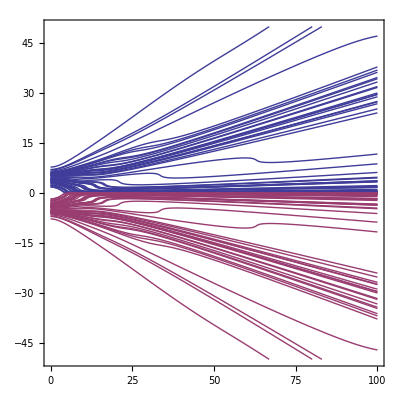

```mathematica
ddd = 5.0;
σσσ = 1.0;
kkk = 2.0;
HollandtablU=Table[NDSolve[{D[y[t], t]==1/(2 kkk)VelocityField[y[t], t, ddd,kkk, σσσ ],y[0]== 5+randomnumnums[[numnum]]},y,{t,0,100}],{numnum,1,50}];
HollandtablD=Table[NDSolve[{D[y[t],t]==1/(2 kkk)VelocityField[y[t], t, ddd,kkk, σσσ ],y[0]== -5-randomnumnums[[numnum]]},y,{t,0,100}],{numnum,1,50}];
Plot[{y[t]/.HollandtablU,y[t]/.HollandtablD},{t,0,100}, PlotRange->{{0,100},{-50,50}},Frame->True,Axes->True,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

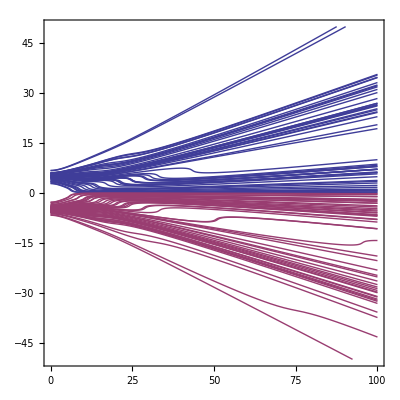

```mathematica
ddd = 5.0;
σσσ = 1.0;
kkk = 2.0;
HollandtablU=Table[NDSolve[{D[y[t], t]==1/(2 kkk)VelocityField[y[t], t, ddd,kkk, σσσ ],y[0]== 5+ RandomVariate[NormalDistribution[0, σσσ]]},y,{t,0,100}],{numnum,1,50}];
HollandtablD=Table[NDSolve[{D[y[t],t]==1/(2 kkk)VelocityField[y[t], t, ddd,kkk, σσσ ],y[0]== -5+RandomVariate[NormalDistribution[0, σσσ]]},y,{t,0,100}],{numnum,1,50}];
Plot[{y[t]/.HollandtablU,y[t]/.HollandtablD},{t,0,100}, PlotRange->{{0,100},{-50,50}},Frame->True,Axes->True,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

```mathematica
AAA = 0.5;
ddd = 5.0;
σσσ = 1.0;
www = 2;
x000 = 0.0;
v000 = 1.0;
kkk= 2;
disss = 0.0;
tmax = 100;
CHUNK = 20;
REPEAT = 50;
CUTTOFF = 70;

outstream=OpenAppend["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/BohmianDataDouble2k.dat"];

Do[
Hollandtabl3DU=Table[NDSolve[{D[y[t], t]==1/(2 kkk)VelocityField[y[t], t, ddd,kkk, σσσ ],y[0]== ddd+RandomVariate[NormalDistribution[0, σσσ]]},y,{t,0,tmax}],{CHUNK}];
Hollandtabl3DD=Table[NDSolve[{D[y[t], t]==1/(2 kkk)VelocityField[y[t], t, ddd,kkk, σσσ ],y[0]== -ddd+RandomVariate[NormalDistribution[0, σσσ]]},y,{t,0,tmax}],{CHUNK}];

TestTableXU[t_] = Flatten[y[t]/.Hollandtabl3DU];
TestTableXD[t_] = Flatten[y[t]/.Hollandtabl3DD];

HistTableAngle = {};
HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt++, If[(TestTableXU[ttt][[NNN]]^2+(ttt-1)^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableXU[ttt][[NNN]]/(ttt-1)]];Break[]]]
]
For[NNN = 1,NNN<=Length[TestTableXD[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt++, If[(TestTableXD[ttt][[NNN]]^2+(ttt-1)^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableXD[ttt][[NNN]]/(ttt-1)]];Break[]]]
];

Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
,{REPEAT}];

Close[outstream]
```

/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/BohmianDataDouble2k.dat

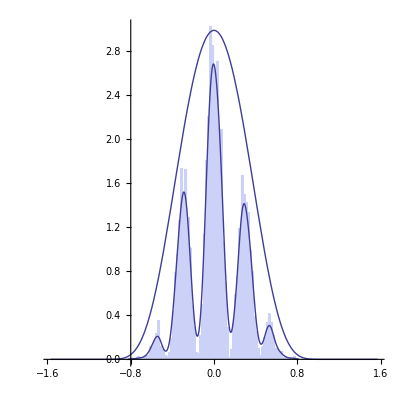

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/BohmianDataDouble2k.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],SmoothHistogram[ReadDataSingle,0.03,PlotStyle->Thick],Plot[2.4(ⅇ^(-Sec[x]^2/0.5^2))/(π Erfc[1/0.5]),{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

```mathematica
Manipulate[Plot[(ⅇ^(-Sec[x]^2/σ^2))/(π Erfc[1/σ]),{x,-π/2,π/2},PlotRange->{Full,{0,4}}],{σ,1,10}]
```

```mathematica
ⅇ^(-k^2 σ^2)
```

ⅇ^(-k^2 σ^2)

```mathematica
Integrate[ⅇ^(-(Tan[x])^2/σ^2 ),{x,-π/2,π/2}]
```

ⅇ^(1/σ^2) π Erfc[1/σ]

```mathematica
FullSimplify[ⅇ^(-(Tan[x])^2/σ^2 )/(ⅇ^(1/σ^2) π Erfc[1/σ])]
```

(ⅇ^(-Sec[x]^2/σ^2))/(π Erfc[1/σ])

```mathematica
Integrate[ⅇ^(ⅈ k x),{x,-d,d}]
```

(2 Sin[d k])/k

```mathematica
Integrate[(ⅇ^(-(x)^2/(4 σ^2)))/((2 π)^(1/4) √σ)ⅇ^(ⅈ k x),{x,-∞,∞}]
```

ConditionalExpression[(2^(3/4) ⅇ^(-k^2 σ^2) π^(1/4))/(√(1/σ^2) √σ),Re[1/σ^2]>0]

```mathematica
Integrate[(2^(3/4) ⅇ^(-k^2 σ^2) π^(1/4))/(√(1/σ^2) √σ)ⅇ^(ⅈ k x + ⅈ k^2 t),{k,-∞,∞}]
```

ConditionalExpression[(ⅇ^(-(ⅈ x^2)/(4 (t+ⅈ σ^2))) (2 π)^(3/4) √(1/σ^2) σ^(3/2))/(√(-ⅈ t+σ^2)),Im[t]+Re[σ^2]>0]

```mathematica
FullSimplify[ⅇ^(-(ⅈ x^2)/(4 (t+ⅈ σ^2))) /(1/(√(σ^2/(2 π t^2+2 π σ^4))))^(1/2)]
```

ⅇ^(-x^2/(4 (-ⅈ t+σ^2))) (σ^2/(2 π t^2+2 π σ^4))^(1/4)

```mathematica
Integrate[ ⅇ^(-x^2/(4 (-ⅈ t+σ^2))) (σ^2/(2 π t^2+2 π σ^4))^(1/4)ⅇ^(-x^2/(4 (ⅈ t+σ^2))) (σ^2/(2 π t^2+2 π σ^4))^(1/4) ,{x,-∞,∞}]
```

ConditionalExpression[1,Re[σ^2/(t^2+σ^4)]>0]

```mathematica
Integrate[ ⅇ^(-(x^2 σ^2)/(2 (t^2+σ^4))) ,{x,-∞,∞}]
```

ConditionalExpression[1/(√(σ^2/(2 π t^2+2 π σ^4))),Re[σ^2/(t^2+σ^4)]>0]

```mathematica
FullSimplify[ⅇ^(-x^2/(4 (-ⅈ t+σ^2))) (σ^2/(2 π t^2+2 π σ^4))^(1/4)ⅇ^(-x^2/(4 (ⅈ t+σ^2))) (σ^2/(2 π t^2+2 π σ^4))^(1/4)]
```

ⅇ^(-(x^2 σ^2)/(2 (t^2+σ^4))) √(σ^2/(2 π t^2+2 π σ^4))

```mathematica
Manipulate[Plot[ⅇ^(-(x^2 σ^2)/(2 (t^2+σ^4))) √(σ^2/(2 π t^2+2 π σ^4)),{x,-20,20},PlotRange->All],{t,0,10},{σ,4,10}]
```

```mathematica
Integrate[Sinc[d k]ⅇ^(ⅈ k x + ⅈ k^2 t),{k,-∞,∞}]
```

ConditionalExpression[1/(24 d Abs[t]^(5/2))√(π/2) (ⅈ t (12 (d-x) Abs[t] HypergeometricPFQ[{1/4},{1/2,5/4},-(d-x)^4/(64 t^2)]+12 (d+x) Abs[t] HypergeometricPFQ[{1/4},{1/2,5/4},-(d+x)^4/(64 t^2)]-(d-x)^3 HypergeometricPFQ[{3/4},{3/2,7/4},-(d-x)^4/(64 t^2)]-(d+x)^3 HypergeometricPFQ[{3/4},{3/2,7/4},-(d+x)^4/(64 t^2)])+Abs[t] (12 (d-x) Abs[t] HypergeometricPFQ[{1/4},{1/2,5/4},-(d-x)^4/(64 t^2)]+12 (d+x) Abs[t] HypergeometricPFQ[{1/4},{1/2,5/4},-(d+x)^4/(64 t^2)]+(d-x)^3 HypergeometricPFQ[{3/4},{3/2,7/4},-(d-x)^4/(64 t^2)]+(d+x)^3 HypergeometricPFQ[{3/4},{3/2,7/4},-(d+x)^4/(64 t^2)])),d∈Reals&&t∈Reals&&x∈Reals]

```mathematica
FullSimplify[1/(24 d Abs[t]^(5/2))√(π/2) (ⅈ t (12 (d-x) Abs[t] HypergeometricPFQ[{1/4},{1/2,5/4},-(d-x)^4/(64 t^2)]+12 (d+x) Abs[t] HypergeometricPFQ[{1/4},{1/2,5/4},-(d+x)^4/(64 t^2)]-(d-x)^3 HypergeometricPFQ[{3/4},{3/2,7/4},-(d-x)^4/(64 t^2)]-(d+x)^3 HypergeometricPFQ[{3/4},{3/2,7/4},-(d+x)^4/(64 t^2)])+Abs[t] (12 (d-x) Abs[t] HypergeometricPFQ[{1/4},{1/2,5/4},-(d-x)^4/(64 t^2)]+12 (d+x) Abs[t] HypergeometricPFQ[{1/4},{1/2,5/4},-(d+x)^4/(64 t^2)]+(d-x)^3 HypergeometricPFQ[{3/4},{3/2,7/4},-(d-x)^4/(64 t^2)]+(d+x)^3 HypergeometricPFQ[{3/4},{3/2,7/4},-(d+x)^4/(64 t^2)]))]
```

1/(2 d √t √Abs[t])π (t (FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)]) (1-ⅈ Sign[t]) Sign[t]+FresnelC[(d-x)/(√(2 π) √t)] (t+ⅈ t Sign[t])+FresnelC[(d+x)/(√(2 π) √t)] (t+ⅈ t Sign[t]))

```mathematica
FullSimplify[1/(2 d √t √t)π (t (FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)]) (1-ⅈ ) +FresnelC[(d-x)/(√(2 π) √t)] (t+ⅈ t )+FresnelC[(d+x)/(√(2 π) √t)] (t+ⅈ t ))]
```

((1/2+ⅈ/2) π (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)]-ⅈ (FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])))/d

```mathematica
FullSimplify[(1/d(1/2+ⅈ/2) π (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)]-ⅈ (FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])))(1/d(1/2-ⅈ/2) π (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)]+ⅈ (FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])))]
```

(π^2 ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2))/(2 d^2)

```mathematica
Sign[-1]^2
```

1

```mathematica
(π^2 t (2 (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2 t-2 Abs[t] (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)]) (FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)]) (-1+1)+t (FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2 (1+1)))/(4 d^2  t  t)
```

1/(4 d^2 t)π^2 (2 t (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+2 t (FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2)

```mathematica
FullSimplify[1/(4 d^2 t)π^2 (2 t (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+2 t (FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2)]
```

(π^2 ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2))/(2 d^2)

```mathematica
Integrate[(π^2 ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2))/(2 d^2),{x,-∞,∞}]
```

$Aborted

```mathematica
Manipulate[Plot[{1/(2 d^2)π^2 ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2),1/(2 d^2)π^2 Sinc[x/d]^2},{x,-20,20},PlotRange->All],{t,0.1,10},{d,4,10}]
```

```mathematica
FullSimplify[D[(π^2 ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2))/(2 d^2),x,x]/((π^2 ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2))/(2 d^2))]
```

```mathematica
themonkeysingle[x_,t_,d_] :=(π^2 ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2))/(2 d^2)
```

```mathematica
FullSimplify[ⅈ(D[(1/d(1/2-ⅈ/2) π (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)]+ⅈ (FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)]))),x](1/d(1/2+ⅈ/2) π (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)]-ⅈ (FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])))-D[(1/d(1/2+ⅈ/2) π (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)]-ⅈ (FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)]))),x](1/d(1/2-ⅈ/2) π (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)]+ⅈ (FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)]))))/(1/(2 d^2)π^2 ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2))]
```

-(2 √(2/π) Sin[(d x)/(2 t)] (Cos[(d^2+x^2)/(4 t)] (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)]) Sin[(d^2+x^2)/(4 t)]))/(√t ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2))

```mathematica
monkeybutts[x_,t_,d_] := -(2 √(2/π) Sin[(d x)/(2 t)] (Cos[(d^2+x^2)/(4 t)] (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)]) Sin[(d^2+x^2)/(4 t)]))/(√t ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2))
```

```mathematica
monkeybutts3[x_,t_,d_] := -( Sin[(d x)/(2 t)] (Cos[(d^2+x^2)/(4 t)] (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)]) Sin[(d^2+x^2)/(4 t)]))/(√t ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2))
```

```mathematica
(√2 ⅇ^(-(4 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) k σ (ⅇ^((2 k^2 (d-x)^2 σ^2)/(z^2+4 k^2 σ^4))+ⅇ^((2 k^2 (d+x)^2 σ^2)/(z^2+4 k^2 σ^4))+2 ⅇ^((2 k^2 (d^2+x^2) σ^2)/(z^2+4 k^2 σ^4)) Cos[(2 d k x z)/(z^2+4 k^2 σ^4)]))/((2+2 ⅇ^(-d^2/(2 σ^2))) √(π z^2+4 k^2 π σ^4))
```

```mathematica
monkeybutts2[x_,t_,d_,k_] := -(2 √(2/π) Sin[(k d x)/(2 t)] (Cos[(k^2(d^2+x^2))/(4 t)] (FresnelC[(k(d-x))/(√(2 π) √t)]+FresnelC[(k(d+x))/(√(2 π) √t)])+(FresnelS[(k(d-x))/(√(2 π) √t)]+FresnelS[(k(d+x))/(√(2 π) √t)]) Sin[(k^2(d^2+x^2))/(4 t)]))/(√t ((FresnelC[(k(d-x))/(√(2 π) √t)]+FresnelC[(k(d+x))/(√(2 π) √t)])^2+(FresnelS[(k(d-x))/(√(2 π) √t)]+FresnelS[(k(d+x))/(√(2 π) √t)])^2))
```

$Aborted

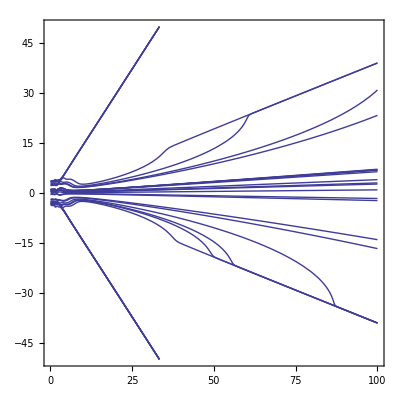

```mathematica
ddd = 5.0;
σσσ = 4.0;
kkk = 2.0;
HollandtablU=Table[NDSolve[{D[y[t], t]==-2/1 monkeybutts2[y[t], t,  σσσ,kkk ],y[0.1]==  RandomVariate[UniformDistribution[{-4,4}]]},y,{t,0.1,100}],{30}];
Plot[{y[t]/.HollandtablU},{t,0.1,100}, PlotRange->{{0.1,100},{-50,50}},Frame->True,Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

```mathematica
On[General::infy]
```

```mathematica
FresnelS[ComplexInfinity]
```

Indeterminate

```mathematica
FresnelS[(k(d-x))/(√(2 π) 0)]
```

Power::infy: Infinite expression 1/0 encountered.

Indeterminate

$Aborted

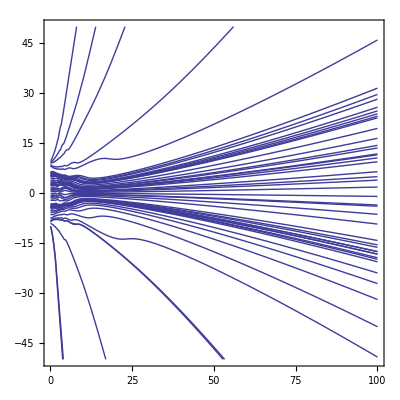

```mathematica
ddd = 10.0;
σσσ = 10.0;
kkk = 2.0;
HollandtablU=Table[NDSolve[{D[y[t], t]==-1/1 monkeybutts3[y[t], t,  σσσ ],y[0.1]==  RandomVariate[UniformDistribution[{-10,10}]]},y,{t,0.1,100}],{50}];
Plot[{y[t]/.HollandtablU},{t,0.1,100}, PlotRange->{{0.1,100},{-50,50}},Frame->True,Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

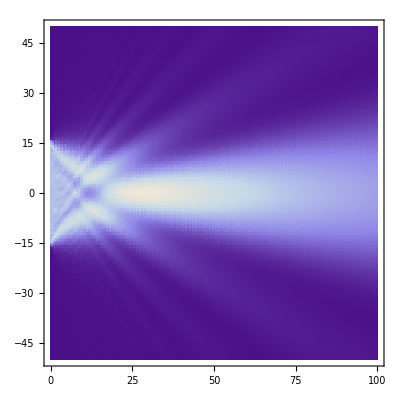

```mathematica
DensityPlot[themonkeysingle[x,t,16],{t,0,100},{x,-50,50},PlotPoints->{100,100},PlotRange->{Full,Full,{0,0.1}},ClippingStyle->Automatic,BaseStyle->{FontFamily->"Times",FontSize->14},AspectRatio->1]
```

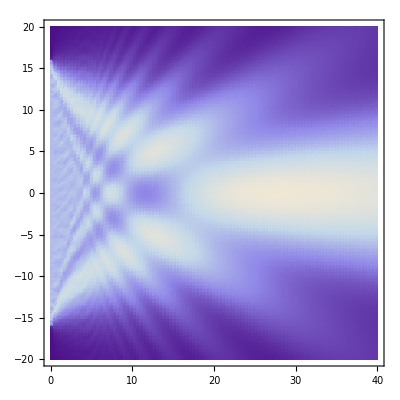

```mathematica
DensityPlot[themonkeysingle[x,t,16],{t,0,40},{x,-20,20},PlotPoints->{100,100},PlotRange->{Full,Full,All},ClippingStyle->Automatic,BaseStyle->{FontFamily->"Times",FontSize->14},AspectRatio->1]
```

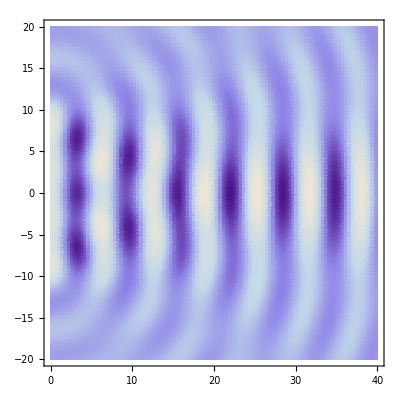

```mathematica
DensityPlot[Sum[BesselJ[0,√(x^2+(y-d)^2)],{d,-10,10}],{x,0,40},{y,-20,20},PlotPoints->{100,100},PlotRange->{Full,Full,All},ClippingStyle->Automatic,BaseStyle->{FontFamily->"Times",FontSize->14},AspectRatio->1]
```

```mathematica
Integrate[BesselJ[0,k √(x^2+y^2)] Cos[w t]+BesselY[0,k √(x^2+y^2)] Sin[w t],{y,-d,d}]
```

∫_-d^d (BesselJ[0,k √(x^2+y^2)] Cos[t w]+BesselY[0,k √(x^2+y^2)] Sin[t w])ⅆy

```mathematica
(√(k/z))/(√(2 π))ⅇ^(-(ⅈ π)/4+ⅈ k z)Integrate[(1)ⅇ^((ⅈ k (x-xp)^2)/(2 z)),{xp,-d,d}]
```

((1/2-ⅈ/2) ⅇ^(-(ⅈ π)/4+ⅈ k z) √(k/z) √(z/k) (Erfi[(1/2+ⅈ/2) (d-x) √(k/z)]+Erfi[(1/2+ⅈ/2) (d+x) √(k/z)]))/(√2)

```mathematica
FullSimplify[((1/2-ⅈ/2) ⅇ^(-(ⅈ π)/4+ⅈ k z) √(k/z) √(z/k) (Erfi[(1/2+ⅈ/2) (d-x) √(k/z)]+Erfi[(1/2+ⅈ/2) (d+x) √(k/z)]))/(√2)]
```

-1/2 ⅈ ⅇ^(ⅈ k z) (Erfi[(1/2+ⅈ/2) (d-x) √(k/z)]+Erfi[(1/2+ⅈ/2) (d+x) √(k/z)])

```mathematica
FullSimplify[(-1/2 ⅈ ⅇ^(ⅈ k z) (Erfi[(1/2+ⅈ/2) (d-x) √(k/z)]+Erfi[(1/2+ⅈ/2) (d+x) √(k/z)]))*]
```

1/2 ⅇ^(-ⅈ k z) (Erf[(1/2+ⅈ/2) (d-x) √(k/z)]+Erf[(1/2+ⅈ/2) (d+x) √(k/z)])

```mathematica
FullSimplify[(-1/2 ⅈ ⅇ^(ⅈ k z) (Erfi[(1/2+ⅈ/2) (d-x) √(k/z)]+Erfi[(1/2+ⅈ/2) (d+x) √(k/z)]))(1/2 ⅇ^(-ⅈ k z) (Erf[(1/2+ⅈ/2) (d-x) √(k/z)]+Erf[(1/2+ⅈ/2) (d+x) √(k/z)]))]
```

-1/4 ⅈ (Erf[(1/2+ⅈ/2) (d-x) √(k/z)]+Erf[(1/2+ⅈ/2) (d+x) √(k/z)]) (Erfi[(1/2+ⅈ/2) (d-x) √(k/z)]+Erfi[(1/2+ⅈ/2) (d+x) √(k/z)])

```mathematica
FullSimplify[ⅈ(D[(-1/2 ⅈ ⅇ^(ⅈ k z) (Erfi[(1/2+ⅈ/2) (d-x) √(k/z)]+Erfi[(1/2+ⅈ/2) (d+x) √(k/z)])),x](1/2 ⅇ^(-ⅈ k z) (Erf[(1/2+ⅈ/2) (d-x) √(k/z)]+Erf[(1/2+ⅈ/2) (d+x) √(k/z)]))-(-1/2 ⅈ ⅇ^(ⅈ k z) (Erfi[(1/2+ⅈ/2) (d-x) √(k/z)]+Erfi[(1/2+ⅈ/2) (d+x) √(k/z)]))D[(1/2 ⅇ^(-ⅈ k z) (Erf[(1/2+ⅈ/2) (d-x) √(k/z)]+Erf[(1/2+ⅈ/2) (d+x) √(k/z)])),x])/(-1/4 ⅈ (Erf[(1/2+ⅈ/2) (d-x) √(k/z)]+Erf[(1/2+ⅈ/2) (d+x) √(k/z)]) (Erfi[(1/2+ⅈ/2) (d-x) √(k/z)]+Erfi[(1/2+ⅈ/2) (d+x) √(k/z)]))]
```

((1-ⅈ) ⅇ^(-(ⅈ k (d^2+x^2))/z) (ⅇ^((ⅈ k (d-x)^2)/(2 z))-ⅇ^((ⅈ k (d+x)^2)/(2 z))) √(k/z) (ⅇ^((ⅈ k (d^2+x^2))/z) (Erf[(1/2+ⅈ/2) (d-x) √(k/z)]+Erf[(1/2+ⅈ/2) (d+x) √(k/z)])+Erfi[(1/2+ⅈ/2) (d-x) √(k/z)]+Erfi[(1/2+ⅈ/2) (d+x) √(k/z)]))/(√π (Erf[(1/2+ⅈ/2) (d-x) √(k/z)]+Erf[(1/2+ⅈ/2) (d+x) √(k/z)]) (Erfi[(1/2+ⅈ/2) (d-x) √(k/z)]+Erfi[(1/2+ⅈ/2) (d+x) √(k/z)]))

```mathematica
Appo[x_,z_,d_,k_] :=((1-ⅈ) ⅇ^(-(ⅈ k (d^2+x^2))/z) (ⅇ^((ⅈ k (d-x)^2)/(2 z))-ⅇ^((ⅈ k (d+x)^2)/(2 z))) √(k/z) (ⅇ^((ⅈ k (d^2+x^2))/z) (Erf[(1/2+ⅈ/2) (d-x) √(k/z)]+Erf[(1/2+ⅈ/2) (d+x) √(k/z)])+Erfi[(1/2+ⅈ/2) (d-x) √(k/z)]+Erfi[(1/2+ⅈ/2) (d+x) √(k/z)]))/(√π (Erf[(1/2+ⅈ/2) (d-x) √(k/z)]+Erf[(1/2+ⅈ/2) (d+x) √(k/z)]) (Erfi[(1/2+ⅈ/2) (d-x) √(k/z)]+Erfi[(1/2+ⅈ/2) (d+x) √(k/z)]))
```

```mathematica
ddd = 10.0;
σσσ = 10.0;
kkk = 1.0;
HollandtablU=Table[NDSolve[{D[y[t], t]==-1/2 Appo[y[t], t,  σσσ,kkk],y[0.1]==  RandomVariate[UniformDistribution[{-10,10}]]},y,{t,0.1,100}],{100}];
Plot[{y[t]/.HollandtablU},{t,0.1,100}, PlotRange->{{0.1,100},{-50,50}},Frame->True,Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.28171.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 4.18203.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 3.4042.

General::stop: Further output of NDSolve :: mxst will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.76864, step size is effectively zero; singularity or stiff system suspected.

Divide::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

NDSolve::njnum: The Jacobian is not a matrix of numbers at {t, y[t]} = {4.33194, -63.1193 + 77.0631\ ⅈ}.

-Graphics-

```mathematica
Manipulate[Plot[((1-ⅈ) ⅇ^(-(ⅈ k (d^2+x^2))/z) (ⅇ^((ⅈ k (d-x)^2)/(2 z))-ⅇ^((ⅈ k (d+x)^2)/(2 z))) √(k/z) (ⅇ^((ⅈ k (d^2+x^2))/z) (Erf[(1/2+ⅈ/2) (d-x) √(k/z)]+Erf[(1/2+ⅈ/2) (d+x) √(k/z)])+Erfi[(1/2+ⅈ/2) (d-x) √(k/z)]+Erfi[(1/2+ⅈ/2) (d+x) √(k/z)]))/(√π (Erf[(1/2+ⅈ/2) (d-x) √(k/z)]+Erf[(1/2+ⅈ/2) (d+x) √(k/z)]) (Erfi[(1/2+ⅈ/2) (d-x) √(k/z)]+Erfi[(1/2+ⅈ/2) (d+x) √(k/z)])),{x,-10,10}],{z,1,20},{d,10,10},{k,1,10}]
```

```mathematica
FullSimplify[Integrate[ Sinc[(k w x)/z]^2,{x,-∞,∞}]]
```

(π z)/(k w)

```mathematica
FullSimplify[Sinc[(k w x)/z]/((π z)/(k w))^(1/2)]
```

(√((k w)/z) Sinc[(k w x)/z])/(√π)

```mathematica
FullSimplify[Sinc[(k w x)/z]^2/((π z)/(k w))]
```

(k w Sinc[(k w x)/z]^2)/(π z)

```mathematica
FraunHoop[x_,z_,w_,k_] := (k w Sinc[(k w x)/z]^2)/(π z)
```

```mathematica
Manipulate[Plot[FraunHoop[x,z,w,k],{x,-10,10},PlotRange->All],{z,1,20},{w,4,10},{k,1,10}]
```

```mathematica
FullSimplify[(ⅈ ⅇ^((ⅈ k (x^2+z^2))/z) √((k w)/z) Sinc[(k w x)/z])/(√π)(-ⅈ ⅇ^((-ⅈ k (x^2+z^2))/z) √((k w)/z) Sinc[(k w x)/z])/(√π)]
```

(k w Sinc[(k w x)/z]^2)/(π z)

```mathematica
Integrate[(ⅈ ⅇ^((ⅈ k x^2)/z+ⅈ k z))/z Sinc[(k w x)/z](-ⅈ ⅇ^((-ⅈ k x^2)/z-ⅈ k z))/z Sinc[(k w x)/z],{x,-∞,∞}]
```

π/(k w z)

```mathematica
FresPoop[x_,z_,w_,k_]:=-(ⅈ ⅇ^((ⅈ k (x^2+z^2))/z) √((k w)/z) Sinc[(k w x)/z])/(√π)
FresPoopCo[x_,z_,w_,k_]:=-(-ⅈ ⅇ^((-ⅈ k (x^2+z^2))/z) √((k w)/z) Sinc[(k w x)/z])/(√π)
```

```mathematica
FullSimplify[ⅈ(D[FresPoop[x,z,w,k],x]FresPoopCo[x,z,w,k]-D[FresPoopCo[x,z,w,k],x]FresPoop[x,z,w,k])/((k w Sinc[(k w x)/z]^2)/(π z))]
```

-(4 k x)/z

```mathematica
Hmmmmmm[x_,t_,d_] :=(ⅇ^((d^2 π^2 x^2)/(2 (d^4+π^4 t^2))) (Cos[(d-x)^2/(4 t)]-Cos[(d+x)^2/(4 t)]-Sin[(d-x)^2/(4 t)]+Sin[(d+x)^2/(4 t)]))/(d √π √((d t)/(d^4+π^4 t^2)))
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 0.228976.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 0.209891.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 74.6055.

General::stop: Further output of NDSolve :: mxst will be suppressed during this calculation.

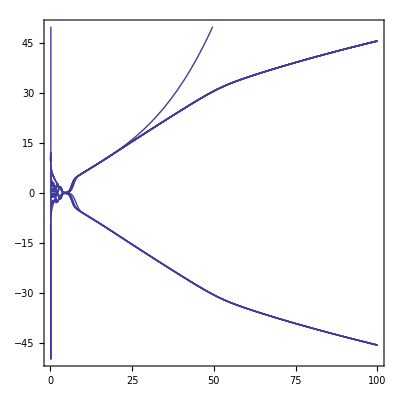

```mathematica
ddd = 10.0;
σσσ = 10.0;
kkk = 1.0;
HollandtablU=Table[NDSolve[{D[y[t], t]==-Hmmmmmm[y[t],t,ddd],y[0.1]==  RandomVariate[UniformDistribution[{-10,10}]]},y,{t,0.1,100}],{20}];
Plot[{y[t]/.HollandtablU},{t,0.1,100}, PlotRange->{{0.1,100},{-50,50}},Frame->True,Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

```mathematica
FullSimplify[ⅈ Integrate[Sin[d k] ⅇ^(ⅈ k x+ⅈ k^2 t),{k,-∞,∞}]]
```

-((1/2+ⅈ/2) ⅇ^(-(ⅈ (d+x)^2)/(4 t)) (-1+ⅇ^((ⅈ d x)/t)) √(π/2))/(√t)

```mathematica
FullSimplify[ⅈ Integrate[Sin[d k] ⅇ^(-ⅈ k x-ⅈ k^2 t),{k,-∞,∞}]]
```

-((1/2-ⅈ/2) ⅇ^((ⅈ (d-x)^2)/(4 t)) (-1+ⅇ^((ⅈ d x)/t)) √(π/2))/(√t)

```mathematica
Simplify[2(-(1/2+ⅈ/2)  (-1 ⅇ^(-(ⅈ (d+x)^2)/(4 t))+Simplify[ⅇ^(-(ⅈ (d+x)^2)/(4 t))ⅇ^((ⅈ d x)/t)]) -(1/2-ⅈ/2)  (-1 ⅇ^((ⅈ (d-x)^2)/(4 t))+Simplify[ⅇ^((ⅈ (d-x)^2)/(4 t))ⅇ^((ⅈ d x)/t)]) )]
```

(1+ⅈ) ⅇ^(-(ⅈ (d^2+x^2))/(2 t)) (ⅇ^((ⅈ (d-x)^2)/(4 t))-ⅇ^((ⅈ (d+x)^2)/(4 t))) (1-ⅈ ⅇ^((ⅈ (d^2+x^2))/(2 t)))

```mathematica
Simplify[2(-(1/2+ⅈ/2)  (-1 ⅇ^(-(ⅈ (d+x)^2)/(4 t))+Simplify[ⅇ^(-(ⅈ (d+x)^2)/(4 t))ⅇ^((ⅈ d x)/t)]))]
```

(-1-ⅈ) (ⅇ^(-(ⅈ (d-x)^2)/(4 t))-ⅇ^(-(ⅈ (d+x)^2)/(4 t)))

```mathematica
Simplify[2(-(1/2-ⅈ/2)  (-1 ⅇ^((ⅈ (d-x)^2)/(4 t))+Simplify[ⅇ^((ⅈ (d-x)^2)/(4 t))ⅇ^((ⅈ d x)/t)]) )]
```

(1-ⅈ) (ⅇ^((ⅈ (d-x)^2)/(4 t))-ⅇ^((ⅈ (d+x)^2)/(4 t)))

```mathematica
Simplify[(-1-ⅈ) (ⅇ^(-(ⅈ (d-x)^2)/(4 t))-ⅇ^(-(ⅈ (d+x)^2)/(4 t)))+(1-ⅈ) (ⅇ^((ⅈ (d-x)^2)/(4 t))-ⅇ^((ⅈ (d+x)^2)/(4 t)))]
```

```mathematica
(1+ⅈ)  (ⅇ^((ⅈ (d-x)^2)/(4 t))-ⅇ^((ⅈ (d+x)^2)/(4 t))) (1 ⅇ^(-(ⅈ (d^2+x^2))/(2 t))-ⅈ Simplify[ⅇ^(-(ⅈ (d^2+x^2))/(2 t)) ⅇ^((ⅈ (d^2+x^2))/(2 t))])
```

(1+ⅈ) (ⅇ^((ⅈ (d-x)^2)/(4 t))-ⅇ^((ⅈ (d+x)^2)/(4 t))) (-ⅈ+ⅇ^(-(ⅈ (d^2+x^2))/(2 t)))

```mathematica
FullSimplify[ExpToTrig[(1+ⅈ) (ⅇ^((ⅈ (d-x)^2)/(4 t))-ⅇ^((ⅈ (d+x)^2)/(4 t))) (-ⅈ+ⅇ^(-(ⅈ (d^2+x^2))/(2 t)))]]
```

-2 ⅈ (Cos[(d-x)^2/(4 t)]-Cos[(d+x)^2/(4 t)]-Sin[(d-x)^2/(4 t)]+Sin[(d+x)^2/(4 t)])

```mathematica
FullSimplify[-((1/2+ⅈ/2) ⅇ^(-(ⅈ (d+x)^2)/(4 t)) (-1+ⅇ^((ⅈ d x)/t)) √(π/2))/(√t)-((1/2-ⅈ/2) ⅇ^((ⅈ (d-x)^2)/(4 t)) (-1+ⅇ^((ⅈ d x)/t)) √(π/2))/(√t)]
```

-((1/2-ⅈ/2) ⅇ^(-(ⅈ (d+x)^2)/(4 t)) (-1+ⅇ^((ⅈ d x)/t)) (ⅈ+ⅇ^((ⅈ (d^2+x^2))/(2 t))) √(π/2))/(√t)

```mathematica
-((1/2-ⅈ/2)  (-1 ⅇ^(-(ⅈ (d+x)^2)/(4 t))+Simplify[ⅇ^(-(ⅈ (d+x)^2)/(4 t))ⅇ^((ⅈ d x)/t)]) (ⅈ+ⅇ^((ⅈ (d^2+x^2))/(2 t))) √(π/2))/(√t)
```

-((1/2-ⅈ/2) (ⅇ^(-(ⅈ (d-x)^2)/(4 t))-ⅇ^(-(ⅈ (d+x)^2)/(4 t))) (ⅈ+ⅇ^((ⅈ (d^2+x^2))/(2 t))) √(π/2))/(√t)

```mathematica
-((1/2-ⅈ/2) ⅇ^(-(ⅈ (d+x)^2)/(4 t)) (-1+ⅇ^((ⅈ d x)/t)) (ⅈ+ⅇ^((ⅈ (d^2+x^2))/(2 t))) √(π/2))/(√t)
```

```mathematica
Sin[d k] ⅇ^(ⅈ k x+ⅈ k^2 t)
```

ⅇ^(ⅈ k^2 t+ⅈ k x) Sin[d k]

```mathematica
Sin[d k] ⅇ^(-ⅈ k x-ⅈ k^2 t)Sin[d k] ⅇ^(ⅈ k x+ⅈ k^2 t)
```

Sin[d k]^2

```mathematica
FullSimplify[]
```

```mathematica
-((1/2-ⅈ/2) (ExpToTrig[ⅇ^(-(ⅈ (d-x)^2)/(4 t))-ⅇ^(-(ⅈ (d+x)^2)/(4 t))]) √(π/2))/(√t)
```

-((1/2-ⅈ/2) √(π/2) (Cos[(d-x)^2/(4 t)]-Cos[(d+x)^2/(4 t)]-ⅈ Sin[(d-x)^2/(4 t)]+ⅈ Sin[(d+x)^2/(4 t)]))/(√t)

```mathematica
FullSimplify[Integrate[ⅇ^(-k^2 d^2-ⅈ k x-ⅈ k^2 t),{k,-∞,∞}]]
```

(ⅇ^(-x^2/(4 d^2+4 ⅈ t)) √π)/(√(d^2+ⅈ t))

```mathematica
FullSimplify[Integrate[ⅇ^(-k^2 d^2+ⅈ k x+ⅈ k^2 t),{k,-∞,∞}]]
```

(ⅇ^(-x^2/(4 d^2-4 ⅈ t)) √π)/(√(d^2-ⅈ t))

```mathematica
FullSimplify[ⅇ^(-x^2/(4 d^2+4 ⅈ t))ⅇ^(-x^2/(4 d^2-4 ⅈ t))]
```

ⅇ^(-(d^2 x^2)/(2 (d^4+t^2)))

```mathematica
Integrate[(Sin[d k]/k)^2,{k,-∞,∞}]
```

d π

```mathematica
Sin[d (π/d)]
```

0

```mathematica
ⅇ^(-k^2/((π/d))^2)
```

ⅇ^(-(d^2 k^2)/π^2)

```mathematica
Integrate[ⅇ^(-(d^2 k^2)/π^2),{k,-∞,∞}]
```

π^(3/2)/d

```mathematica
Manipulate[Plot[{(Sin[π d k]/k)^2/(d π),ⅇ^(-(d^2 k^2)/π^2)/(π^(3/2)/d)},{k,-5,5},PlotRange->All],{d,1,10}]
```

```mathematica
Integrate[ⅇ^(-(d^2 k^2)/π^2+ⅈ k x+i k^2 t),{k,-∞,∞}]
```

ConditionalExpression[(ⅇ^(x^2/(4 (-d^2/π^2+i t))) π^(3/2))/(√(d^2-i π^2 t)),π^2 t Re[i]<d^2]

```mathematica
FullSimplify[Integrate[Sinc[d k]^2,{k,-∞,∞}]]
```

π/d

```mathematica
FullSimplify[Sinc[d k]/√(π/d)]
```

(√d Sinc[d k])/(√π)

```mathematica
FullSimplify[(√d Sinc[d k])/(√π)(k)]
```

Sin[d k]/(√d √π)

```mathematica
FullSimplify[ⅈ Integrate[Sin[d k]/(√d √π) ⅇ^(ⅈ k x+ⅈ k^2 t),{k,-∞,∞}]]
```

-((1/2+ⅈ/2) ⅇ^(-(ⅈ (d+x)^2)/(4 t)) (-1+ⅇ^((ⅈ d x)/t)))/(√2 √(d t))

```mathematica
-((1/2+ⅈ/2)  (-1 ⅇ^(-(ⅈ (d+x)^2)/(4 t))+Simplify[ⅇ^(-(ⅈ (d+x)^2)/(4 t))ⅇ^((ⅈ d x)/t)]))/(√2 √(d t))
```

-((1/2+ⅈ/2) (ⅇ^(-(ⅈ (d-x)^2)/(4 t))-ⅇ^(-(ⅈ (d+x)^2)/(4 t))))/(√2 √(d t))

```mathematica
FullSimplify[-ⅈ Integrate[Sin[d k]/(√d √π) ⅇ^(-ⅈ k x-ⅈ k^2 t),{k,-∞,∞}]]
```

((1/2-ⅈ/2) ⅇ^((ⅈ (d-x)^2)/(4 t)) (-1+ⅇ^((ⅈ d x)/t)))/(√2 √(d t))

```mathematica
((1/2-ⅈ/2)  (-1 ⅇ^((ⅈ (d-x)^2)/(4 t))+Simplify[ⅇ^((ⅈ (d-x)^2)/(4 t))ⅇ^((ⅈ d x)/t)]))/(√2 √(d t))
```

((1/2-ⅈ/2) (-ⅇ^((ⅈ (d-x)^2)/(4 t))+ⅇ^((ⅈ (d+x)^2)/(4 t))))/(√2 √(d t))

```mathematica
FullSimplify[ⅈ(-((1/2+ⅈ/2) (ⅇ^(-(ⅈ (d-x)^2)/(4 t))-ⅇ^(-(ⅈ (d+x)^2)/(4 t))))/(√2 √(d t))-((1/2-ⅈ/2) (-ⅇ^((ⅈ (d-x)^2)/(4 t))+ⅇ^((ⅈ (d+x)^2)/(4 t))))/(√2 √(d t)))]
```

((1/2+ⅈ/2) ⅇ^(-(ⅈ (d^2+x^2))/(2 t)) (ⅇ^((ⅈ (d-x)^2)/(4 t))-ⅇ^((ⅈ (d+x)^2)/(4 t))) (ⅈ+ⅇ^((ⅈ (d^2+x^2))/(2 t))))/(√2 √(d t))

```mathematica
((1/2+ⅈ/2)  (ⅇ^((ⅈ (d-x)^2)/(4 t))-ⅇ^((ⅈ (d+x)^2)/(4 t))) (ⅈ ⅇ^(-(ⅈ (d^2+x^2))/(2 t))+Simplify[ⅇ^(-(ⅈ (d^2+x^2))/(2 t))ⅇ^((ⅈ (d^2+x^2))/(2 t))]))/(√2 √(d t))
```

((1/2+ⅈ/2) (ⅇ^((ⅈ (d-x)^2)/(4 t))-ⅇ^((ⅈ (d+x)^2)/(4 t))) (1+ⅈ ⅇ^(-(ⅈ (d^2+x^2))/(2 t))))/(√2 √(d t))

```mathematica
FullSimplify[ExpToTrig[((1/2+ⅈ/2) (ⅇ^((ⅈ (d-x)^2)/(4 t))-ⅇ^((ⅈ (d+x)^2)/(4 t))) (1+ⅈ ⅇ^(-(ⅈ (d^2+x^2))/(2 t))))/(√2 √(d t))]]
```

(Cos[(d-x)^2/(4 t)]-Cos[(d+x)^2/(4 t)]-Sin[(d-x)^2/(4 t)]+Sin[(d+x)^2/(4 t)])/(√2 √(d t))

```mathematica
FullSimplify[((Cos[(d-x)^2/(4 t)]-Cos[(d+x)^2/(4 t)]-Sin[(d-x)^2/(4 t)]+Sin[(d+x)^2/(4 t)])/(√2 √(d t)))/((d ⅇ^(-(d^2 π^2 x^2)/(2 (d^4+π^4 t^2))) √(π/2))/(√(d^4+π^4 t^2)))]
```

(ⅇ^((d^2 π^2 x^2)/(2 (d^4+π^4 t^2))) (Cos[(d-x)^2/(4 t)]-Cos[(d+x)^2/(4 t)]-Sin[(d-x)^2/(4 t)]+Sin[(d+x)^2/(4 t)]))/(d √π √((d t)/(d^4+π^4 t^2)))

```mathematica
Integrate[ ⅇ^(-(d^2 k^2)/(2 π^2)) ,{k,-∞,∞}]
```

(√2 π^(3/2))/d

```mathematica
FullSimplify[ⅇ^(-(d^2 k^2)/π^2)((√2 π^(3/2))/d)^(-1/2)]
```

(√d ⅇ^(-(d^2 k^2)/π^2))/(2^(1/4) π^(3/4))

```mathematica
Integrate[(√d ⅇ^(-(d^2 k^2)/π^2))/(2^(1/4) π^(3/4))ⅇ^(+ⅈ k x+ⅈ k^2 t),{k,-∞,∞}]
```

(ⅇ^(-(π^2 x^2)/(4 (d^2-ⅈ π^2 t))) π^(3/4))/(2^(1/4) √(d-(ⅈ π^2 t)/d))

```mathematica
Integrate[(√d ⅇ^(-(d^2 k^2)/π^2))/(2^(1/4) π^(3/4))ⅇ^(-ⅈ k x-ⅈ k^2 t),{k,-∞,∞}]
```

(ⅇ^(-(π^2 x^2)/(4 (d^2+ⅈ π^2 t))) π^(3/4))/(2^(1/4) √(d+(ⅈ π^2 t)/d))

```mathematica
FullSimplify[(ⅇ^(-(π^2 x^2)/(4 (d^2-ⅈ π^2 t))))(ⅇ^(-(π^2 x^2)/(4 (d^2+ⅈ π^2 t))))/((√(2/π) √(d^4+π^4 t^2))/d)]
```

(d ⅇ^(-(d^2 π^2 x^2)/(2 (d^4+π^4 t^2))) √(π/2))/(√(d^4+π^4 t^2))

```mathematica
Integrate[(d ⅇ^(-(d^2 π^2 x^2)/(2 (d^4+π^4 t^2))) √(π/2))/(√(d^4+π^4 t^2)),{x,-∞,∞}]
```

1

```mathematica
FullSimplify[(-((1/2+ⅈ/2) (ⅇ^(-(ⅈ (d-x)^2)/(4 t))-ⅇ^(-(ⅈ (d+x)^2)/(4 t))))/(√2 √(d t)))/((ⅇ^(-(π^2 x^2)/(4 (d^2-ⅈ π^2 t))) π^(3/4))/(2^(1/4) √(d-(ⅈ π^2 t)/d)))]
```

-((1/2+ⅈ/2) ⅇ^((π^2 x^2)/(4 (d^2-ⅈ π^2 t))) (ⅇ^(-(ⅈ (d-x)^2)/(4 t))-ⅇ^(-(ⅈ (d+x)^2)/(4 t))) √(-(ⅈ π^2)/d^2+1/t))/(2^(1/4) π^(3/4))

```mathematica
FullSimplify[(((1/2-ⅈ/2) (-ⅇ^((ⅈ (d-x)^2)/(4 t))+ⅇ^((ⅈ (d+x)^2)/(4 t))))/(√2 √(d t)))/((ⅇ^(-(π^2 x^2)/(4 (d^2+ⅈ π^2 t))) π^(3/4))/(2^(1/4) √(d+(ⅈ π^2 t)/d)))]
```

((1/2-ⅈ/2) ⅇ^((π^2 x^2)/(4 (d^2+ⅈ π^2 t))) (-ⅇ^((ⅈ (d-x)^2)/(4 t))+ⅇ^((ⅈ (d+x)^2)/(4 t))) √((ⅈ π^2)/d^2+1/t))/(2^(1/4) π^(3/4))

```mathematica
FullSimplify[-((1/2+ⅈ/2) ⅇ^((π^2 x^2)/(4 (d^2-ⅈ π^2 t))) (ⅇ^(-(ⅈ (d-x)^2)/(4 t))-ⅇ^(-(ⅈ (d+x)^2)/(4 t))) √(-(ⅈ π^2)/d^2+1/t))/(2^(1/4) π^(3/4))-((1/2-ⅈ/2) ⅇ^((π^2 x^2)/(4 (d^2+ⅈ π^2 t))) (-ⅇ^((ⅈ (d-x)^2)/(4 t))+ⅇ^((ⅈ (d+x)^2)/(4 t))) √((ⅈ π^2)/d^2+1/t))/(2^(1/4) π^(3/4))]
```

-((-1)^(1/4) ⅇ^((d (d^3+2 d^2 x-2 ⅈ π^2 t x+d (-ⅈ π^2 t+x^2)))/(4 t (ⅈ d^2+π^2 t))) (-1+ⅇ^((ⅈ d x)/t)) (√(d^2-ⅈ π^2 t)-ⅈ ⅇ^((ⅈ d^2 (1+(d^2 x^2)/(d^4+π^4 t^2)))/(2 t)) √(d^2+ⅈ π^2 t)))/(d (2 π)^(3/4) √t)

```mathematica
-1/(d (2 π)^(3/4) √t)(-1)^(1/4)  (-1 ⅇ^((d (d^3+2 d^2 x-2 ⅈ π^2 t x+d (-ⅈ π^2 t+x^2)))/(4 t (ⅈ d^2+π^2 t)))+Simplify[ⅇ^((d (d^3+2 d^2 x-2 ⅈ π^2 t x+d (-ⅈ π^2 t+x^2)))/(4 t (ⅈ d^2+π^2 t)))ⅇ^((ⅈ d x)/t)]) (√(d^2-ⅈ π^2 t)-ⅈ ⅇ^((ⅈ d^2 (1+(d^2 x^2)/(d^4+π^4 t^2)))/(2 t)) √(d^2+ⅈ π^2 t))
```

```mathematica
-1/(d (2 π)^(3/4) √t) ⅇ^((d (d^3+d (-ⅈ π^2 t+x^2)))/(4 t (ⅈ d^2+π^2 t)))(-ⅇ^((d (2 d^2 x-2 ⅈ π^2 t x))/(4 t (ⅈ d^2+π^2 t)))+ⅇ^((d (-2 d^2 x+2 ⅈ π^2 t x))/(4 t (ⅈ d^2+π^2 t)))) (√(d^2-ⅈ π^2 t)-ⅈ ⅇ^((ⅈ d^2 (1+(d^2 x^2)/(d^4+π^4 t^2)))/(2 t)) √(d^2+ⅈ π^2 t))
```

```mathematica
-1/(d (2 π)^(3/4) √t) (-ⅇ^((d (2 d^2 x-2 ⅈ π^2 t x))/(4 t (ⅈ d^2+π^2 t)))+ⅇ^((d (-2 d^2 x+2 ⅈ π^2 t x))/(4 t (ⅈ d^2+π^2 t)))) (√(d^2-ⅈ π^2 t)ⅇ^((d (d^3+d (-ⅈ π^2 t+x^2)))/(4 t (ⅈ d^2+π^2 t)))-ⅈ Simplify[ⅇ^((d (d^3+d (-ⅈ π^2 t+x^2)))/(4 t (ⅈ d^2+π^2 t)))ⅇ^((ⅈ d^2 (1+(d^2 x^2)/(d^4+π^4 t^2)))/(2 t)) ] √(d^2+ⅈ π^2 t))
```

```mathematica
-1/(d (2 π)^(3/4) √t)(-ⅇ^((d (2 d^2 x-2 ⅈ π^2 t x))/(4 t (ⅈ d^2+π^2 t)))+ⅇ^((d (-2 d^2 x+2 ⅈ π^2 t x))/(4 t (ⅈ d^2+π^2 t)))) Simplify[(ⅇ^((d (d^3+d (-ⅈ π^2 t+x^2)))/(4 t (ⅈ d^2+π^2 t))) √(d^2-ⅈ π^2 t)-ⅈ ⅇ^((ⅈ d^2 (d^2+ⅈ π^2 t+x^2))/(4 t (d^2+ⅈ π^2 t))) √(d^2+ⅈ π^2 t))]
```

-((-ⅇ^((d (2 d^2 x-2 ⅈ π^2 t x))/(4 t (ⅈ d^2+π^2 t)))+ⅇ^((d (-2 d^2 x+2 ⅈ π^2 t x))/(4 t (ⅈ d^2+π^2 t)))) (ⅇ^((d^2 (d^2-ⅈ π^2 t+x^2))/(4 t (ⅈ d^2+π^2 t))) √(d^2-ⅈ π^2 t)-ⅈ ⅇ^((ⅈ d^2 (d^2+ⅈ π^2 t+x^2))/(4 t (d^2+ⅈ π^2 t))) √(d^2+ⅈ π^2 t)))/(d (2 π)^(3/4) √t)

```mathematica
FullSimplify[ExpToTrig[-1/(d (2 π)^(3/4) √t)(-ⅇ^((d (2 d^2 x-2 ⅈ π^2 t x))/(4 t (ⅈ d^2+π^2 t)))+ⅇ^((d (-2 d^2 x+2 ⅈ π^2 t x))/(4 t (ⅈ d^2+π^2 t)))) (ⅇ^((d^2 (d^2-ⅈ π^2 t+x^2))/(4 t (ⅈ d^2+π^2 t))) √(d^2-ⅈ π^2 t)-ⅈ ⅇ^((ⅈ d^2 (d^2+ⅈ π^2 t+x^2))/(4 t (d^2+ⅈ π^2 t))) √(d^2+ⅈ π^2 t))]]
```

```mathematica
-((ⅇ^((d^2 (d^2-ⅈ π^2 t+x^2))/(4 t (ⅈ d^2+π^2 t))) √(d^2-ⅈ π^2 t)-ⅈ ⅇ^((ⅈ d^2 (d^2+ⅈ π^2 t+x^2))/(4 t (d^2+ⅈ π^2 t))) √(d^2+ⅈ π^2 t)) Sin[(d x)/(2 t)])/(d π^(3/4) √t)
```

```mathematica
-((ⅇ^((d^2 (d^2-ⅈ π^2 t+x^2))/(4 t (ⅈ d^2+π^2 t))) √(d^2-ⅈ π^2 t)-ⅈ ⅇ^((- d^2 (d^2+ⅈ π^2 t+x^2))/(4 t (ⅈ d^2- π^2 t))) √(d^2+ⅈ π^2 t)) Sin[(d x)/(2 t)])/(d π^(3/4) √t)
```

-((ⅇ^((d^2 (d^2-ⅈ π^2 t+x^2))/(4 t (ⅈ d^2+π^2 t))) √(d^2-ⅈ π^2 t)-ⅈ ⅇ^(-(d^2 (d^2+ⅈ π^2 t+x^2))/(4 t (ⅈ d^2-π^2 t))) √(d^2+ⅈ π^2 t)) Sin[(d x)/(2 t)])/(d π^(3/4) √t)

```mathematica
ExpToTrig[-((ⅇ^((d^2 (d^2-ⅈ π^2 t+x^2))/(4 t (ⅈ d^2+π^2 t))) √(d^2-ⅈ π^2 t)-ⅈ ⅇ^(-(d^2 (d^2+ⅈ π^2 t+x^2))/(4 t (ⅈ d^2-π^2 t))) √(d^2+ⅈ π^2 t)) Sin[(d x)/(2 t)])/(d π^(3/4) √t)]
```

-(√(d^2-ⅈ π^2 t) Cosh[(d^2 (d^2-ⅈ π^2 t+x^2))/(4 t (ⅈ d^2+π^2 t))] Sin[(d x)/(2 t)])/(d π^(3/4) √t)+(ⅈ √(d^2+ⅈ π^2 t) Cosh[(d^2 (d^2+ⅈ π^2 t+x^2))/(4 t (ⅈ d^2-π^2 t))] Sin[(d x)/(2 t)])/(d π^(3/4) √t)-(√(d^2-ⅈ π^2 t) Sin[(d x)/(2 t)] Sinh[(d^2 (d^2-ⅈ π^2 t+x^2))/(4 t (ⅈ d^2+π^2 t))])/(d π^(3/4) √t)-(ⅈ √(d^2+ⅈ π^2 t) Sin[(d x)/(2 t)] Sinh[(d^2 (d^2+ⅈ π^2 t+x^2))/(4 t (ⅈ d^2-π^2 t))])/(d π^(3/4) √t)

```mathematica
ExpToTrig[-((ⅇ^((d^2 (d^2-ⅈ π^2 t+x^2))/(4 t (ⅈ d^2+π^2 t))) -ⅈ ⅇ^(-(d^2 (d^2+ⅈ π^2 t+x^2))/(4 t (ⅈ d^2-π^2 t))) ) Sin[(d x)/(2 t)])/(d π^(3/4) √t)]
```

-(Cosh[(d^2 (d^2-ⅈ π^2 t+x^2))/(4 t (ⅈ d^2+π^2 t))] Sin[(d x)/(2 t)])/(d π^(3/4) √t)+(ⅈ Cosh[(d^2 (d^2+ⅈ π^2 t+x^2))/(4 t (ⅈ d^2-π^2 t))] Sin[(d x)/(2 t)])/(d π^(3/4) √t)-(Sin[(d x)/(2 t)] Sinh[(d^2 (d^2-ⅈ π^2 t+x^2))/(4 t (ⅈ d^2+π^2 t))])/(d π^(3/4) √t)-(ⅈ Sin[(d x)/(2 t)] Sinh[(d^2 (d^2+ⅈ π^2 t+x^2))/(4 t (ⅈ d^2-π^2 t))])/(d π^(3/4) √t)

```mathematica
Integrate[ⅇ^(ⅈ k^2 t+ⅈ k x) Sinc[d k],{k,-∞,∞}]
```

((1/2+ⅈ/2) π (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)]-ⅈ (FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])))/d

```mathematica
NDSolve[{D[ψ[k],k]==ⅇ^(ⅈ k^2 t+ⅈ k x) Sinc[ k],ψ[0]==0},ψ,{k,-10,10}]
```

NDSolve::nlnum: The function value {1.\ ⅇ^(0.  + 1.04324×10^-8\ ⅈ)\ t - (0.  + 0.000102139\ ⅈ)\ x} is not a list of numbers with dimensions {1} at {k, ψ[k]} = {-0.000102139, -0.000102139}.

NDSolve::nlnum: The function value {1.\ ⅇ^(0.  + 1.04324×10^-8\ ⅈ)\ t + (0.  + 0.000102139\ ⅈ)\ x} is not a list of numbers with dimensions {1} at {k, ψ[k]} = {0.000102139, 0.000102139}.

{{ψ→InterpolatingFunction[{{0.,0.}},<>]}}

```mathematica
Norm[NIntegrate[ⅇ^(ⅈ k^2 2+ⅈ k 2) Sinc[ k],{k,-∞,∞}]]
```

1.20093

```mathematica
ght = Table[(Norm[NIntegrate[ⅇ^(ⅈ k^2 (t+1.9)+ⅈ k( x-100)) Sinc[4 k],{k,-∞,∞}]])(Norm[NIntegrate[ⅇ^(ⅈ k^2 (t+1.9)+ⅈ k( x-100)) Sinc[4 k],{k,-∞,∞}]]),{t,20},{x,200}];
```

```mathematica
ghtsmall = Table[(Norm[NIntegrate[ⅇ^(ⅈ k^2 (1.9)+ⅈ k( 2x-100)) Sinc[4 k],{k,-∞,∞}]]),{x,10}];
```

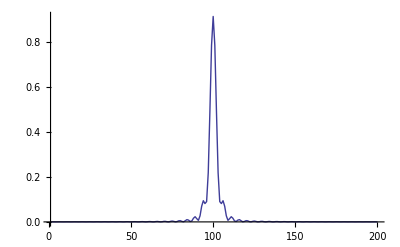

```mathematica
ListLinePlot[ght[[1]],PlotRange->All]
```

```mathematica
Animate[ListLinePlot[ght[[pp]],PlotRange->All],{pp,1,20,1}]
```